```mathematica
(*Series Approaximation for Solving Diif. Eq.s*)
(*Examples :- Solve the diff. eq of SHO by using the Technique of Series Approaximation.. *)
(* its a Local sol.(approaximate sol.) not global*)
(*Define Diff. eq.*)
deq=x''[t]+ω^2 x[t]==0;
t0=0;n=10;
(*Generate a Power Series ,,,,,, x[t] is a sol. here, so generate for it.*)

series=Series[x[t],{t,t0,n-1}];    (* ==================*)
(*put the series into the differential eq.*)
sereq=deq/.{x[t]->series,x''[t]->D[series,{t,2}]};(*Series of eq.s = Linear combination of Eq.
all Coefficients of Linearly independent variable =0 *)
(*In Power Series No eq < no of Unknowns (x[0], x'[0], x''[0],,,*)
(*Def two additional  eq. by using initial conditions.*)
initialconds={x[t0]==4,x'[t0]==0};
eqs=Join[initialconds,{sereq}];(*it Joints Two lists.*)
(* Generate list of Unknowns*)
unknowns=Table[Derivative[order][x][t0],{order,0,n-1}];
unknowns=Solve[eqs,unknowns];
(*Put thecoefficients into  Series.*)
series=series/.unknowns[[1]];
(*Convert the series into polynomials*)
(*Radius of convergence increases as no of terms increases.*)
ω=20;                             (* ==================*)
polyn=Normal[series];
Plot[polyn,{t,0,2*2Pi/ω},PlotStyle->{{Red,Thick}}];
```

No of Unknowns

{y[0],y'[0],y''[0],y^(3)[0],y^(4)[0],y^(5)[0],y^(6)[0],y^(7)[0],y^(8)[0],y^(9)[0],y^(10)[0],y^(11)[0],y^(12)[0],y^(13)[0],y^(14)[0],y^(15)[0],y^(16)[0],y^(17)[0],y^(18)[0],y^(19)[0]}

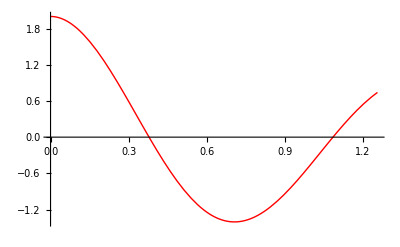

```mathematica
(*Problem:- Compute and Plot the Sol. of the diff.eq by using the Technique of Series Approaximation..with I.C => y[0]=2;y'[0]=0;    y''[t]+ 20 y[t]=0 *)
Deq=y''[t]+y'[t]+ 20 y[t]==0 ;
ser=Series[y[t],{t,t0,n-1}];
sereq=Deq/.{y[t]->ser,y'[t]->D[ser,t],y''[t]->D[ser,{t,2}]};

iniCond={y[t0]==2,y'[t0]==0};
eq=Join[iniCond,{sereq}];
"No of Unknowns"
unknown=Table[Derivative[i][y][t0],{i,0,n-1}](* ==================*)
ser=ser/.Solve[eq,unknown][[1]];     (* ==================*)
pol=Normal[ser];
Plot[pol,{t,0,2Pi/5},PlotStyle->{{Red,Thick}}]
```